# Adam’s Big Notebook

This document contains a summary of the code/results that I obtained while working with the Rey/Regal group in the year 2013. If there are any confusions, or typos, please email me at adam.green@colorado.edu. You can see the latest version of this notebook at github: https://github.com/ringstadd/gaussianwellrey. 

Thank you for a great year, I learned a lot.

## Parameters

```mathematica
ℏ=1.05457*10^-34;
λ=852.0*10^-9;
ks=(2π)/λ; (*wavevector for the short lattice*)
kl=π/λ; (*wavevector for the long lattice*)
a=λ/2;  (*short lattice spacing*)
amu=1.6605*10^-27;
mRb=86.909*amu;  (*mass or Rb87*)
Er=(ℏ^2 ks^2)/(2mRb); (*Recoil energy of the short lattice*)
as=5.3*10^-9;   (*approximate s-wave scattering length for Rb87 (in meters)*)
λ=852.0*10^-9;
ks=(2π)/λ;
Er=N[(ℏ^2 ks^2)/(2mRb)];
btwn=.9*10^-6;
waist=.75*10^-6;
Vt=Er/(ℏ^2/(mRb*waist^2))//N
```

15.2958

## Visualizations

### 1D Bound States

Visualize the bound states of a double well: 1D:

```mathematica
F[x_,V1_,V2_,b_]:=-V1*Vt*Exp[-2*(x-b/2)^2]-V1*Vt*Exp[-2*(x+b/2)^2];
FC[x_,V1_,V2_,b_]:=-V1*Er*Exp[-2*(x-b/(2))^2]-V2*Er*Exp[-2*(x+b/2)^2];
```

#### Documentation F[]

```mathematica
(*Vt is a scaling factor. The original equation is ℏ^2/(2*m)d^2/dx^2+V*Exp(-2*(x-b/2)^2/c^2) = E. However, because functions work with dimensionaless things (avoid overflow/underflow errors), we can work on length scales where c = 1. So, we can factor out a length scale from x, and Arg[Exp] becomes -2*(χ*r-b/2)^2/c^2, then set χ=c, then Arg[Exp] becomes -2(r-b/(2*c))^2, and the rest of the equation becomes:
d^2/(2 dr^2)+V*m*c^2/ℏ^2*Exp[] = 0. Since Adam's code works with potentials in units of recoil energies (ie. 100 Er), it becomes expediant just to calculate Vt=Er/E', where E' = ℏ^2/(m*c^2). *)
(*V is the prefactor*recoil units that will give you the depth of your potential. b will be the interwell seperation. This will construct a symmetric potential.*)
```

```mathematica
Manipulate[Plot[FC[x,V1,V2,b]/(2*π*ℏ),{x,-3,3}],{V1,0,V2+20*Vt},{b,0,2}]
```

#### Calculate the enegy levels for a given configuration:

```mathematica
(*E =computePlaneMatrix2Well[V,(*c=*).5,b,length of box, or wavelenth of largest plane wave,numberofbasisstates,numberofstates] *)
EnergyasB[V_,p_,L_,n_,bend_]:= Table[{b,computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,L,p,n][[1]]*Er/Vt/(2*π*ℏ)},{b,0,bend,.1}]
```

#### Documentation EnergyasB[]

V is the prefactor * the recoil energy of the well depth. ‘p’ is the number of basis states, 200 is usually a good bet, but when in doubt use the converg function to test convergence! L is the length of the box. As a rule of thumb, your largest wavelength will be L2. Your smallest wavelength will be 2L/200, so with p=200, and an L of 10, the smallest wavelength you get is .1 in units of the waist. So, you need to make sure that your resolution is smaller than the smallest feature you are trying to resolve (probably the wannier functions). So, this resolution should AT LEAST be as small as the b. However, there are other subtle length scales: because of the periodic nature of the boundary conditions, we can get into a situation where if you have two wells, that are well seperated, they can reach through the periodic boundary conditions to tunnel into each other through the boundary. So, you need to make sure that the boundary is far enough away that that tunneling rate is negligible. Also, there is one last convergence issues: In the analytical calculations that I did, I assumed that the length of the box is inifinite. This allowed very easy/fast formulas for mathematica. I have checked this, and it is small compared to the other factors. Rule of thumb, work with a large box size, but the larger the box size, the larger number of basis states you need to take.

#### Visualize Bound States for Given b

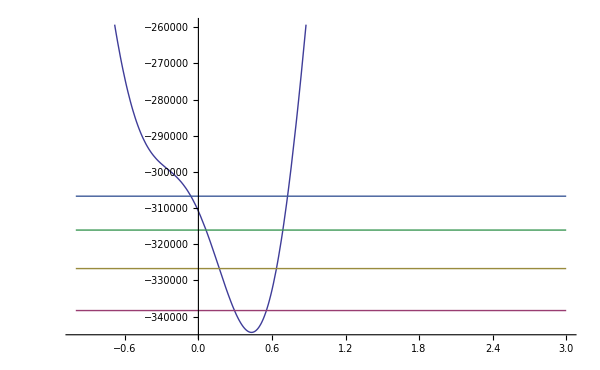

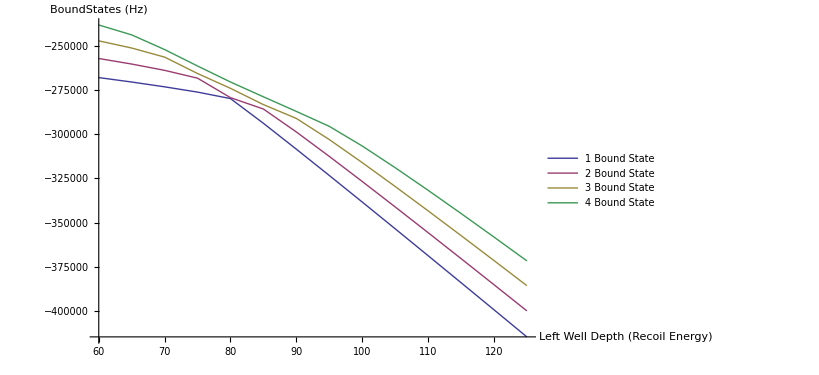

```mathematica
b=1.1;
V1=100; (*V1 and V2 measured in Energy recoil units as defined in parameters*)
V2=80;
basisnum=100;
length = 12; (*Length of the 'box' that defines the periodic boundary conditions*)
energylevels = 4;

bound = Re[computePlaneMatrix2WellBias[V1*Vt,V2*Vt,.5,b/2.,length,basisnum,energylevels][[1]]*Er/Vt/(2*π*ℏ)];
Plot[{FC[x,V1,V2,b]/(2*π*ℏ),bound},{x,-1,3},PlotRange->{Automatic}]
Vlist={60,65,70,75,80,85,90,95,100,105,110,115,120,125};
boundlist = Map[ Re[computePlaneMatrix2WellBias[Vt*#,V2*Vt,.5,b/2.,length,basisnum,energylevels][[1]]*Er/Vt/(2*π*ℏ)] &,Vlist];
ListLinePlot[Map[Transpose[{Vlist,Transpose[boundlist][[#]]}]&,Range[energylevels]],AxesLabel->{"Left Well Depth (Recoil Energy)","BoundStates (Hz)"},PlotLegends->{Map[StringJoin[ToString[#]," Bound State"]&,Range[energylevels]]}]
```

#### Visualize Bound States for Range of b

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

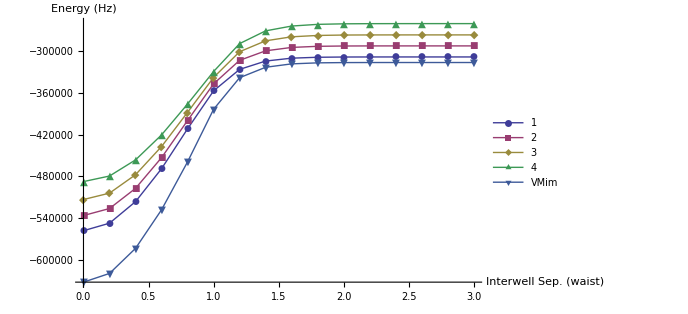

{The convergence of basis states E(p+1)-E(p) is given by:,{-0.00186884}}

```mathematica
V1=Vt*100;
V2=Vt*80;
numberofbasisstates=100;
LengthofBox=12;
energylevel=4;
bmax=3;
L1 = Table[{b,(computePlaneMatrix2WellBias[V1,V2,.5,b/2.,LengthofBox,numberofbasisstates,energylevel][[1]])},{b,0,bmax,.2}];
E1 = Table[{L1[[p]][[1]],L1[[p]][[2]][[1]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
E2 = Table[{L1[[p]][[1]],L1[[p]][[2]][[2]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
E3 = Table[{L1[[p]][[1]],L1[[p]][[2]][[3]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
E4 = Table[{L1[[p]][[1]],L1[[p]][[2]][[4]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
Vmin = Table[{b,FindMinimum[F[x,100,80,b],{x,1.1}][[1]]*Er/Vt/(2*π*ℏ)},{b,0,bmax,.2}];
Manipulate[Plot[FC[x,V1,V2,b]/(2*π*ℏ),{x,-3,3}],{b,0,bmax}]
ListLinePlot[{E1,E2,E3,E4,Vmin},PlotLegends->{1,2,3,4,"VMim"},PlotMarkers->Automatic,AxesLabel->{"Interwell Sep. (waist)","Energy (Hz)"}]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2WellBias[V1,V2,.5,1.5/2.,LengthofBox,numberofbasisstates+1,1][[1]]-computePlaneMatrix2WellBias[V1,V2,.5,1.5/2.,LengthofBox,numberofbasisstates,1][[1]])}
```

This plot shows several features: The blue-triangle is the minimum value of the potential (this will be the energy value of the bottom of the well. The rest are the bound states of the system.

### 2D Visualization

{The convergence of basis states E(p+1)-E(p) is given by:,{12.7259}}

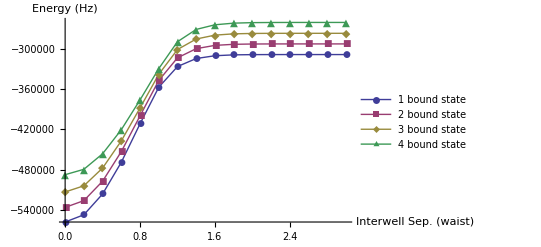

```mathematica
V1 = 100*Vt;
V2=80*Vt;
numberofbasisstates=20;
Lengthofbox=9;

L2d1 = Table[{b,Eigenvalues[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates,b/2.]-10000000.*IdentityMatrix[numberofbasisstates^2],4]+10000000},{b,0,3,.2}];
E2d1 = Table[{L1[[p]][[1]],L2d1[[p]][[2]][[1]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
E2d2 = Table[{L1[[p]][[1]],L2d1[[p]][[2]][[2]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
E2d3 = Table[{L1[[p]][[1]],L2d1[[p]][[2]][[3]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
E2d4 = Table[{L1[[p]][[1]],L2d1[[p]][[2]][[4]]*Er/Vt/(2*π*ℏ)},{p,1,Length[L1]}];
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(Eigenvalues[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates,1.2/2.]-10000000.*IdentityMatrix[numberofbasisstates^2],1]-Eigenvalues[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates+1,1.2/2.]-10000000.*IdentityMatrix[(numberofbasisstates+1)^2],1])}
ListLinePlot[{E1,E2,E3,E4},PlotLegends->{Map[StringJoin[ToString[#]," bound state"]&,Range[4]]},PlotMarkers->Automatic,AxesLabel->{"Interwell Sep. (waist)","Energy (Hz)"}]
```

### WaveFunction and Wannier Functions

```mathematica
(*First, visualize the wavefunction for 2D*)
V1 = 100*Vt;
V2=80*Vt;
numberofbasisstates=20;
Lengthofbox=9;
b=1;
WE = Eigensystem[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates,b/2.]-1000.*IdentityMatrix[numberofbasisstates^2],2];
Plot3D[Abs[groundState[WE[[2]][[1]],Lengthofbox,x,y]]^2,{x,-3,3},{y,-3,3},PlotRange->All]
Plot3D[Abs[groundState[WE[[2]][[2]],Lengthofbox,x,y]]^2,{x,-3,3},{y,-3,3},PlotRange->All]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(Eigenvalues[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates,1.2/2.]-10000000.*IdentityMatrix[numberofbasisstates^2],1]-Eigenvalues[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates+1,1.2/2.]-10000000.*IdentityMatrix[(numberofbasisstates+1)^2],1])}
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Now, construct a rough wannier function*)
V1 = 100*Vt;
V2=80*Vt;
numberofbasisstates=20;
Lengthofbox=9;
b=1;
WE = Eigensystem[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates,b/2.]-1000.*IdentityMatrix[numberofbasisstates^2],2];
(*Now, take the eigenvectors, and build the wannier functions*)
WanPsi0 [x_,y_] := groundState[WE[[2]][[1]],Lengthofbox,x,y];
WanPsi1[x_,y_] := groundState[WE[[2]][[2]],Lengthofbox,x,y];
(*Check normalization of the ground and excite state*)
(*previous version of wigmaker failed, as WigPsi0 wasn't always real. Ansatz: WigPsi0 and WigPsi1 are
conjugate related: if Im Psi0 ==0, then Re Psi1 ==0*)

Wan1[x_,y_]:=Wan1[x,y]=(WanPsi0[x,y]+ⅈ*WanPsi1[x,y])/Sqrt[2];
Wan2[x_,y_]:=Wan2[x,y]=(WanPsi0[x,y]-ⅈ*WanPsi1[x,y])/Sqrt[2];
Plot3D[Abs[Wan1[x,y]]^2,{x,-3,3},{y,-3,3},PlotRange->All]
Plot3D[Abs[Wan2[x,y]]^2,{x,-3,3},{y,-3,3},PlotRange->All]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(WE[[1]][[1]]-Eigenvalues[BuildPlaneMatrix2D2WellBias[V1,V2,Lengthofbox,numberofbasisstates+1,1.2/2.]-10000000.*IdentityMatrix[(numberofbasisstates+1)^2],1])}
```

-Graphics3D-

-Graphics3D-

{The convergence of basis states E(p+1)-E(p) is given by:,{9.99886×10^6}}

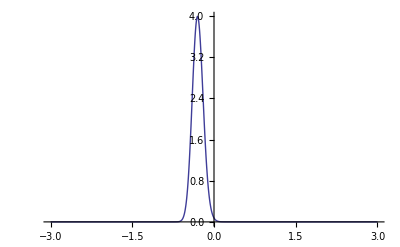

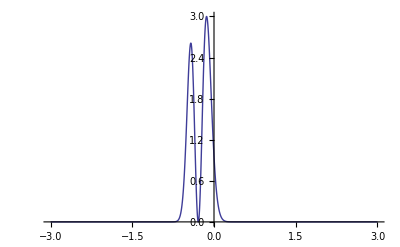

{The convergence of basis states E(p+1)-E(p) is given by:,{1.19209×10^-7}}

```mathematica
(*Now, visualize the wavefunction for 1D*)
V1 = 100*Vt;
V2=80*Vt;
basisnum=100;
length=9;
b=1;
energylevels=2;
WE = computePlaneMatrix2WellBias[V1,V2,.5,b/2.,length,basisnum,energylevels];
Plot[Abs[groundState1D[WE[[2]][[1]],length,x]]^2,{x,-3,3},PlotRange->All]
Plot[Abs[groundState1D[WE[[2]][[2]],length,x]]^2,{x,-3,3},PlotRange->All]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2WellBias[V1,V2,.5,b/2.,length,basisnum+1,1][[1]]-computePlaneMatrix2WellBias[V1,V2,.5,b/2.,length,basisnum,1][[1]])}
```

{{Wig1$1363701},{Wig2$1363701}}

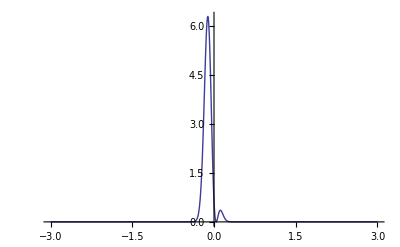

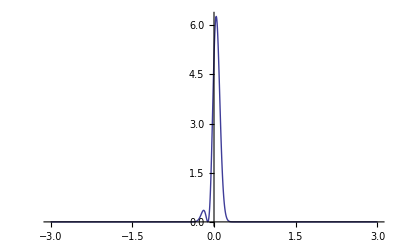

{The convergence of basis states E(p+1)-E(p) is given by:,{1.19209×10^-7}}

```mathematica
(*Now, visualize the wavefunction for 1D*)
V1 = 100*Vt;
V2=80*Vt;
basisnum=100;
length=9;
b=1;
energylevels=2;
WE = computePlaneMatrix2WellBias[V1,V2,.5,b/2.,length,basisnum,energylevels];
(*Now, take the eigenvectors, and build the wannier functions*)
(*Check normalization of the ground and excite state*)
(*previous version of wigmaker failed, as WigPsi0 wasn't always real. Ansatz: WigPsi0 and WigPsi1 are
conjugate related: if Im Psi0 ==0, then Re Psi1 ==0*)
{W1,W2} =findbestwan[V1,V2,b,length,basisnum]
Plot[Abs[W1[[1]][x]]^2,{x,-3,3},PlotRange->All]
Plot[Abs[W2[[1]][x]]^2,{x,-3,3},PlotRange->All]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2WellBias[V1,V2,.5,b/2.,length,basisnum+1,1][[1]]-computePlaneMatrix2WellBias[V1,V2,.5,b/2.,length,basisnum,1][[1]])}
```

## Tunneling

### 1D Tunneling Rates:

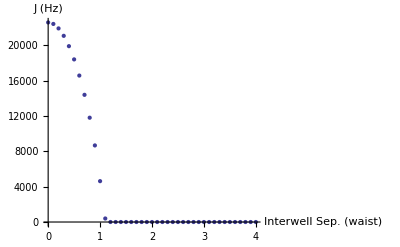

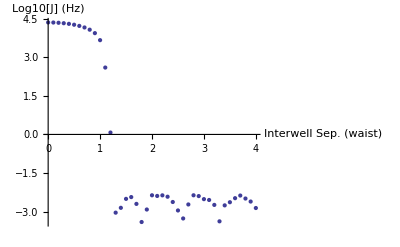

{The convergence of basis states E(p+1)-E(p) is given by:,{4.76837×10^-7}}

```mathematica
V=100*Vt;
numbasis=100;
LengthofBox=9;
OneDTunelChangingB= Table[{b,computePlaneMatrix2Well[V,.5,b/2.,LengthofBox,numbasis,4][[1]][[2]]*Er/Vt/(2*π*ℏ)-computePlaneMatrix2Well[V,.5,b/2.,LengthofBox,numbasis,4][[1]][[1]]*Er/Vt/(2*π*ℏ)},{b,0,4,.1}];
ListPlot[OneDTunelChangingB,AxesLabel->{"Interwell Sep. (waist)","J (Hz)"}]
ListPlot[(OneDTunelChangingB/.{x_,y_}->{x,Log10[y]}),AxesLabel->{"Interwell Sep. (waist)","Log10[J] (Hz)"}]
Convergence=
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numbasis+1,1][[1]]-computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numbasis,1][[1]])}
```

### 2D Tunneling:

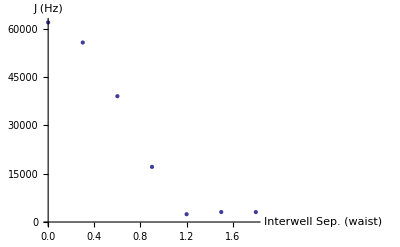

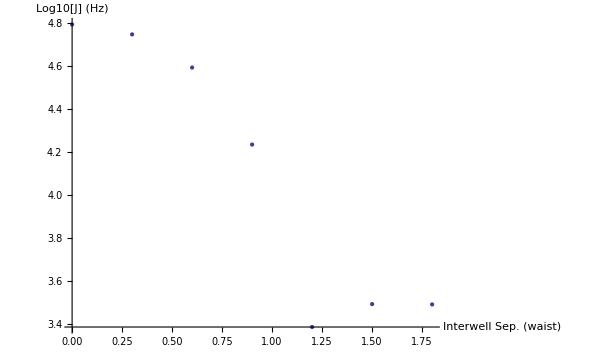

{The convergence of basis states E(p+1)-E(p) is given by:,{-0.332852}}

```mathematica
V=100*Vt;
numbasis=20;
LengthofBox=10;
TwoDTunelChangingB= Table[{b,Tunneling2D[V,LengthofBox,numbasis,b]*Er/Vt/(2*π*ℏ)/2},{b,0,2,.3}];
ListLinePlot[TwoDTunelChangingB,AxesLabel->{"Interwell Sep. (waist)","J (Hz)"}]
ListLinePlot[(TwoDTunelChangingB/.{x_,y_}->{x,Log10[y]}),AxesLabel->{"Interwell Sep. (waist)","Log10[J] (Hz)"}]
Convergence=
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numbasis+1,1][[1]]-computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numbasis,1][[1]])}
```

Note, the seemingly periodic nature is (I beleive), due to noise/convergence issues.When the well’s are well seperated, they will be highly localized due to the strong nature of the potential. You could calculate the width of the wannier function to see if it exceeds .33, which is the current spatial resolution in units of the waist.

### Sinusoid Compared to 1D Tunneling:

```mathematica
Vscale[b_]:=Module[{x,V},
F[x_]:=-Exp[-2*(x-b/2)^2]-Exp[-2*(x+b/2)^2];
V =F[0]-FindMinimum[F[x],{x,b/2}][[1]]
]
```

This function will find the correct height for the sinusoid potential, so that it matches up with the bump height of the double gaussian potential.

```mathematica
beff[b_]:=Module[{x,bef},
F[x_]:=-Exp[-2*(x-b/2)^2]-Exp[-2*(x+b/2)^2];
bef=2*(x/.FindMinimum[F[x],{x,1.1}][[2]])
]
```

This function will find the effective interwell seperation. Because the two gaussian wells will interfere with each other, it will change where the bottom of each well is. This is important, as we need to be able to fit the wavelength of the sinusoid potential to the distance between the bottoms of the wells.

(*Vary the potential depth*)

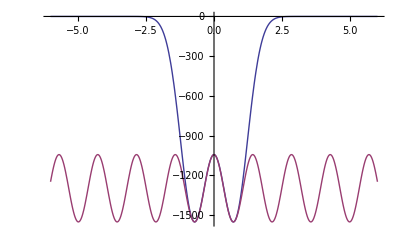

{{0,58.5181},{1,17.7861},{2,5.73985},{3,2.11125},{4,0.861744},{5,0.380503},{6,0.178594},{7,0.0880368},{8,0.045187},{9,0.0239967},{10,0.0131211},{11,0.00735914},{12,0.00422084},{13,0.00246953},{14,0.0014709},{15,0.000890358},{16,0.000546919},{17,0.000340501},{18,0.000214625},{19,0.000136837},{20,0.0000881709},{21,0.0000573761},{22,0.0000376823},{23,0.0000249627},{24,0.0000166713},{25,0.0000112193}}

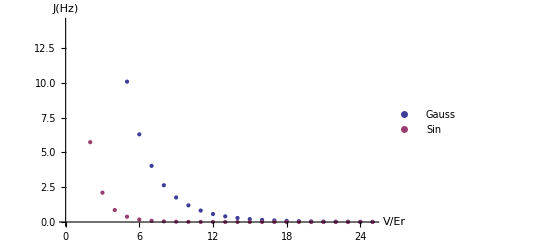

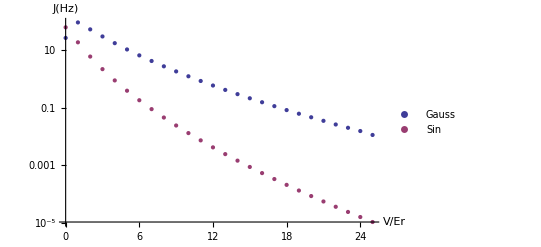

{The convergence of basis states E(p+1)-E(p) is given by:,{-0.229739}}

```mathematica
(*Vary the potential depth*)
b=1.1*10^-6;
V=100;
p=100;(*Number of basis states. Rough: 100 is fine up to around V =100 Vt, depending on waist. For V =700 Vt, you need 300 basis states. Converting into recoils, for V = 46 Er, you need 300 basis states, and higher, depending on the b you are working with. The tunneling rates will start to curve up when it stops converging*)
(*Also, if you make the b less exact, it works better.*)
bscale=b/waist;
Vone=Vscale[bscale];
bone=beff[bscale];
Plot[{F[x,100,100,bscale],(F[0,100,100,bscale]+Vone*Vt*100/2*(-1+Cos[2*π/bone*x]))},{x,-6,6}]
gaustunu1= Table[{V,(computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,9,p,2][[1]][[2]]-
computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,9,p,2][[1]][[1]])*Er/Vt/(2*π*ℏ)/2},{V,0,25,1}];

sintunbu1 = Table[{V,SinTunnel[V*Vone,b*bone]},{V,0,25,1}]
ListPlot[{gaustunu1,sintunbu1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
ListLogPlot[{gaustunu1,sintunbu1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numberofbasisstates+1,1][[1]]-computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numberofbasisstates,1][[1]])}
```

```mathematica
bone
```

1.42209

(*Vary the interwellsep*)

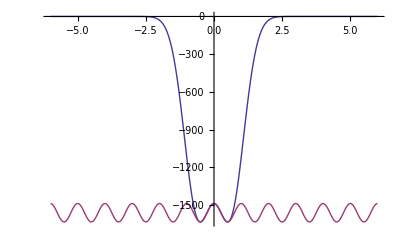

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

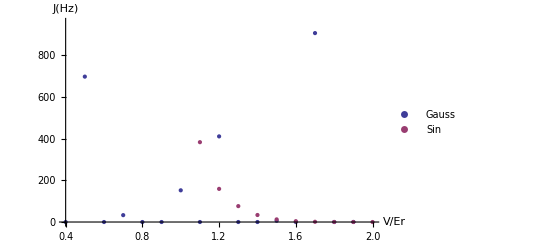

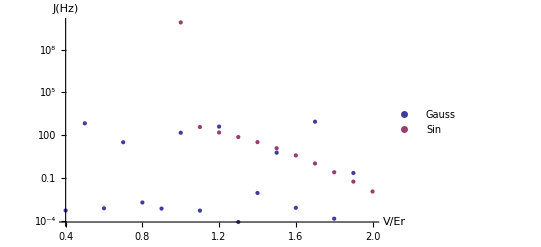

{The convergence of basis states E(p+1)-E(p) is given by:,{0.000734448}}

```mathematica
(*Vary the interwellsep*)
V=1;
b=.9*10^-6;
p=400;(*Number of basis states. Rough: 100 is fine up to around V =100 Vt, depending on waist. For V =700 Vt, you need 300 basis states. Converting into recoils, for V = 46 Er, you need 300 basis states, and higher, depending on the b you are working with. The tunneling rates will start to curve up when it stops converging*)
bscale=b/waist;
Vone=Vscale[bscale];
bone=beff[bscale];

Plot[{F[x,100,100,bscale],(F[0,100,100,bscale]+Vone*Vt*100/2*(-1+Cos[2*π/bone*x]))},{x,-6,6}]
gaustunu1= Table[{b,(computePlaneMatrix2Well[V*Vt,.5,(b/waist)/2.,13,p,2][[1]][[2]]-
computePlaneMatrix2Well[V*Vt,.5,(b/waist)/2.,13,p,2][[1]][[1]])*Er/Vt/(2*π*ℏ)/2},{b,.4,2,.1}];
btable  = Table[{b,Vscale[b],beff[b]},{b,1,2,.1}];
sintunbu1 = Table[{btable[[n]][[1]],SinTunnel[V*btable[[n]][[2]],waist*btable[[n]][[1]]*btable[[n]][[3]] ]},{n,1,Length[btable]}];
ListPlot[{gaustunu1,sintunbu1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
ListLogPlot[{gaustunu1,sintunbu1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
Convergence={"The convergence of basis states E(p+1)-E(p) is given by:",(computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numberofbasisstates+1,1][[1]]-computePlaneMatrix2Well[V,.5,1.5/2.,LengthofBox,numberofbasisstates,1][[1]])}
```

## Functions

```mathematica
Clear[h]
Clear[M]
h = 1.05457173*10^-34;
M = 1.443161*10^-25;
```

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Module[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

HMV1[1,1,0.1,0,0.5]

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Module[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+xIndex[i,size]

```mathematica
kx[6,5]
```

-3+xIndex[6,5]

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
BuildPlaneMatrix2D2WellBias[V1_,V2_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -π*1/(2*L^2)*SparseArray[{i_,j_}->(V1*R2W[kx[j,p]-kx[i,p],L,b]+V2*R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2WellH[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]

]
```

```mathematica
computePlaneMatrix2WellBox[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - 1/2(V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[1/(2 c^2)(-b+ⅈ*c^2(m-l))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length)-1/2(V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[(1/(2 c^2)(b+ⅈ*c^2(m-l))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length);
M = Eigensystem[Table[H[π*l/length,π*m/length],{l,1,p},{m,1,p}]-10000*IdentityMatrix[p],3]

]
```

```mathematica
ComputePlaneWaveEN[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigenvalues[M-10000*IdentityMatrix[p^2],3]
]
```

```mathematica
(-bsep+ⅈ*c^2(l-m))^2//Expand
```

bsep^2-2 ⅈ bsep c^2 l-c^4 l^2+2 ⅈ bsep c^2 m+2 c^4 l m-c^4 m^2

```mathematica
1/2 (k-l) (2 ⅈ bsep+(-k+l) w^2)//Expand
```

ⅈ bsep k-ⅈ bsep l-(k^2 w^2)/2+k l w^2-(l^2 w^2)/2

```mathematica
Tunneling2D[V_,L_,p_,b_]:= Module[{En0,En1, EnList,T},
EnList = Eigenvalues[BuildPlaneMatrix2D2Well[V,L,p,b/2.]-1000.*IdentityMatrix[p^2],2]+1000;
En1 = EnList[[2]];
En0  =EnList [[1]];
T = En1-En0
]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_,numberofstates_]:= Module[{l,m,H,Em,M,norm,Energies},
(*Compute eigenvalues for the gaussian well. Note, for all the work I am doing c=.5, this is because the experimentalists, work with a Exp[-2()^2/c^2], where I defined my c Exp[-()^2/(2*c^2)]. Since I work in units of the waist, c=1, but, by putting it c=.5, I get to pop out the 2 on the top.*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000000*IdentityMatrix[p+1],numberofstates];
Energies = {M[[1]]+1000000000,M[[2;;]][[1]]}
]
```

```mathematica
computePlaneMatrix2WellBias[V1_,V2_,c_,b_,length_,p_,numberofstates_]:= Module[{l,m,H,Em,M,norm,Energies},
(*Compute eigenvalues for the gaussian well. Note, for all the work I am doing c=.5, this is because the experimentalists, work with a Exp[-2()^2/c^2], where I defined my c Exp[-()^2/(2*c^2)]. Since I work in units of the waist, c=1, but, by putting it c=.5, I get to pop out the 2 on the top.*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V1*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V2*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000000*IdentityMatrix[p+1],numberofstates];
Energies = {M[[1]]+1000000000,M[[2;;]][[1]]}
]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

```mathematica
SinTunnel[VEr_,λsi_]:=Module[{Et,Er},
(*The mathieucharateristic function will give the value 'a', corresponding to the equation:
y'' +(a+2*q*Cos[2*z])y = 0. So, one has to get the SWE into a form like this. This is why the Et factor comes in:
h^2/(2*m)d^2 ψ^2/dx^2+V/2*Cos[2*π/λ*x]-E=0 -> d^2 ψ^2/dθ^2+V/2(2*m/(ℏ^2 χ^2))Cos[2*π/λ*χ*θ]-E=0
where χ contains the units and scaling of x. To get the Cos term to look right, this becomes: χ=λ/π, and the equation becomes:
d^2 ψ^2/dθ^2+2(V/4(2*(m*λ^2)/(ℏ^2*π^2)))Cos[2θ]-E*(2*(m*λ^2)/(ℏ^2*π^2))=0, so the term in brackets is the scaling factor Et*)


Er=(ℏ^2 ks^2)/(2mRb);
Et =π^2*ℏ^2/(2*mRb*(λsi)^2);
1/4.(MathieuCharacteristicA[.999,(VEr*Er*1/(4Et))]-MathieuCharacteristicA[0,(VEr*Er*1/(4Et))])*Et/(2*π*ℏ)
]
```

```mathematica
groundState1D[EM_,L_,x_]:=Module[{Size =Length[EM],i},
EMn = Normalize[EM];
Sum[EMn[[i]]*N[Exp[-ⅈ*2.*π/L*ky[i,Size]*x]/Sqrt[L],8],{i,1,Size}]
]
groundState1Dplt[V_,c_,b_,L_,p_]:=Module[{WE,x,gstate,estate},
WE = computePlaneMatrix2Well[V,c,b,L,p];
gstate[x_]:=groundState1D[WE[[2]][[1]],L,x];
estate[x_]:=groundState1D[WE[[2]][[2]],L,x];
{gstate,estate}
]


WigMaker[V_,c_,b_,L_,p_]:=Module[{WE,WigPsi0,WigPsi1,Wig1,Wig2,x,test},
WE = computePlaneMatrix2Well[V,c,b/2.,L,p];
(* WE[[1]]+10000*)

(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_] = groundState1D[WE[[2]][[1]],L,x];
WigPsi1[x_] = groundState1D[WE[[2]][[2]],L,x];
(*Check normalization of the ground and excite state*)
(*previous version of wigmaker failed, as WigPsi0 wasn't always real. Ansatz: WigPsi0 and WigPsi1 are
conjugate related: if Im Psi0 ==0, then Re Psi1 ==0*)

Wig1[x_]:=Wig1[x]=Abs[(WigPsi0[x]+ⅈ*WigPsi1[x])/Sqrt[2]];
Wig2[x_]:=Wig2[x]=Abs[(WigPsi0[x]-ⅈ*WigPsi1[x])/Sqrt[2]];

{Wig1,Wig2,WE[[1]]}
]
WigMakerBias[V1_,V2_,c_,b_,L_,p_,phase_]:=Module[{WE,WigPsi0,WigPsi1,Wig1,Wig2,x,test},
WE = computePlaneMatrix2WellBias[V1,V2,c,b/2.,L,p,2];
(* WE[[1]]+10000*)

(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_] = groundState1D[WE[[2]][[1]],L,x];
WigPsi1[x_] = groundState1D[WE[[2]][[2]],L,x];
(*Check normalization of the ground and excite state*)
(*previous version of wigmaker failed, as WigPsi0 wasn't always real. Ansatz: WigPsi0 and WigPsi1 are
conjugate related: if Im Psi0 ==0, then Re Psi1 ==0*)

Wig1[x_]:=Wig1[x]=Abs[(WigPsi0[x]+Exp[ⅈ*phase]*WigPsi1[x])/Sqrt[2]];
Wig2[x_]:=Wig2[x]=Abs[(WigPsi0[x]+Exp[-ⅈ*phase]WigPsi1[x])/Sqrt[2]];

{Wig1,Wig2}
]
Onsite[V_,c_,b_,L_,p_] := Module[{WE,WigPsi0,WigPsi1,Wig1,Wig2,x,U},
WE = computePlaneMatrix2Well[V,c,b,L,p];
(*WE[[1]]+10000*)
groundState1D[WE[[2]][[1]],12,x];
(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_] = groundState1D[WE[[2]][[1]],12,x];
WigPsi1[x_] = groundState1D[WE[[2]][[2]],12,x];
(*Check normalization of the ground and excite state*)
Wig1[x_]=(WigPsi0[x]+ⅈ*WigPsi1[x])/Sqrt[2];
Wig2[x_]=(WigPsi0[x]-ⅈ*WigPsi1[x])/Sqrt[2];
U =NIntegrate[Abs[Wig1[x]]^4,{x,-L/2,L/2}]
]
(*Now, make a wannier generating function for 2D*)
groundState[EM_,L_,x_,y_]
WanMaker2D[V_,b_,L_,p_]:=Module[{WE,WigPsi0,WigPsi1,Wig1,Wig2,x,test,y},
WE = Eigensystem[BuildPlaneMatrix2D2Well[V,L,p,b/2.]-1000.*IdentityMatrix[p^2],2];

(* WE[[1]]+10000*)
(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_,y_] = groundState[WE[[2]][[1]],L,x,y];
WigPsi1[x_,y_] = groundState[WE[[2]][[2]],L,x,y];
(*Check normalization of the ground and excite state*)
(*previous version of wigmaker failed, as WigPsi0 wasn't always real. Ansatz: WigPsi0 and WigPsi1 are
conjugate related: if Im Psi0 ==0, then Re Psi1 ==0*)

Wig1[x_,y_]:=Wig1[x,y]=Abs[(WigPsi0[x,y]+ⅈ*WigPsi1[x,y])/Sqrt[2]];
Wig2[x_,y_]:=Wig2[x,y]=Abs[(WigPsi0[x,y]-ⅈ*WigPsi1[x,y])/Sqrt[2]];

{Wig1,Wig2,WE[[1]]}
]
width[W1_,W2_]:=Module[{y,y1,y2,w1,width1},
y1=y/.Last[NMaximize[W1[y],y]];
w1 = y/.FindRoot[W1[y]==W1[y1]/2,{y,0}];
width1 =Abs[2*(y1-w1)]
]
distance[W1_,W2_]:=Module[{y,y1,y2},
y1=y/.Last[NMaximize[W1[y],y]];
y2=y/.Last[NMaximize[W2[y],y]];
y1-y2
]
findbestwan[V1_,V2_,b_,L_,numbasis_]:=Module[{W,widthtest,p},
(*Create wan list*)
W = WigMakerBias[V1,V2,.5,b/2,L,numbasis,#]&/@Range[0,2*π,.1];
widthtest=width[#[[1]],#[[2]]]&/@W;
p=Ordering[widthtest,1];
{W[[p,1]],W[[p,2]]}
]
```

2.7182818^(-((0.+6.28319 ⅈ) (-0.2071068 x_-0.2071068 y_))/L_)/(Norm[EM_] L_)

```mathematica
t=WanMaker2D[10,1.5,8,10]
```

{Wig1$253577,Wig2$253577,{-1005.27,-1004.4}}

```mathematica
Plot3D[t[[1]][x,y],{x,-4,4},{y,-4,4},PlotRange->All]
```

-Graphics3D-